# Studio della cinematica di una gru per scarico/carico navi mediante Sintesi

## Funzioni Iniziali per Analisi di Posizione

#### Funzione Quadrilatero

```mathematica
Quadrilatero[q_,xA_,yA_,L1_,L2_,L3_,modo_,xD_,yD_]:= Module[{xB,yB,L5,θ5,cosα,α,θ2,xC,yC,θ3},
xB =xA+L1 Cos[q]; (* si calcola la posizione di B *)
yB = yA+L1 Sin[q];
L5 = √((xD-xB)^2+(yD-yB)^2); (* si calcola la lunghezza del lato BD *)
θ5 = ArcTan[xD-xB,yD-yB]; (* si calcola l'angolo θ5: notare l'uso della funzione arcotangente a due argomenti *)
cosα= (L5^2+L2^2-L3^2)/(2 L5 L2); (* teorema del coseno: si calcola l'argomento del coseno *)
α = 1;
If[Abs[cosα]≤1,
If[modo>0,α =1,α = -1] (* meccanismo si assembla *)
,
If[modo>0,α =1,α = -1] (* non si assembla e α è un numero complesso *)
];
θ2 = θ5-α*ArcCos[cosα]; (* si calcola θ2 *)
xC= xB + L2 Cos[θ2]; (* si trova il punto C *)
yC= yB + L2 Sin[θ2];
θ3 = ArcTan[xD-xC,yD-yC]; (* si calcola θ3: notare l'uso della funzione arcotangente a due argomenti *)
{θ2,θ3,{{xA,yA},{xB,yB},{xC,yC},{xD,yD}}} (* si restituisce θ3,θ2 e il poligono ABCD *)
]
```

#### Funzione Trilatero per Estremo P e Peso K

```mathematica
Trilatero[θ1_,θ2_,LA_,LB_,xC_,yC_]:= {{LA Cos[θ1],LA Sin[θ1]},{LA Cos[θ1]+LB Cos[θ2],LA Sin[θ1]+LB Sin[θ2]},{xC,yC}}
```

#### Definizione Valori

```mathematica
var=
{xA=0,
yA=0,
L1=10,
L2=13,
L6=5,
xD=-7.5,
yD=13,
L3=25,
L4=5,
L5=30,
L1P=18,
L2P=25,
L1K=10,
L2K=10,
θ1noto=π/6,
θ2noto=π/6,
θ0=ArcTan[xD,yD],
L0=√(xD^2+yD^2)};
modo1=-1;
modo2=1;
v1=1;
v2=2;
```

```mathematica
L11=12.2;
L22=13.7;
L33=23.8;
L44=5.2;
L55=33.9;
L66=6.6;
xDD=-11;
yDD=8.7;
```

#### Determino le posizini dei qudrilateri

```mathematica
Pol1[pol1_]:=Quadrilatero[pol1,xA,yA,Lv1,Lv2,Lv6,modo2,xvD,yvD]
Pol2[pol2_]:=Quadrilatero[pol2,
							Pol1[pol2][[3,2,1]],
							Pol1[pol2][[3,2,2]],Lv3,Lv4,Lv5,modo2,
							Pol1[pol2][[3,3,1]],
							Pol1[pol2][[3,3,2]]]
```

#### Posizione P

```mathematica
Pol3[pol3_]:=Trilatero[pol3,Pol2[pol3][[1]]+π+θ1noto,Lv1+Lv3,LvP,
						Pol2[pol3][[3,3,1]],Pol2[pol3][[3,3,2]]		
						]
```

```mathematica
Pol4[pol4_]:=Trilatero[ArcTan[xvD,yvD],Pol1[pol4][[2]]-θ2noto,√(xvD^2+yvD^2),L1K,Pol1[pol4][[3,3,1]],Pol1[pol4][[3,3,2]]]
```

## Sintesi di Traiettoria con Correlazione

Definisco gli estremi di un range nel quale campionare gli angoli su cui valutare la funzione penalità

```mathematica
qmax = (4589 π)/12000;
qmin = (8089 π)/36000;
```

Punti di Accuratezza

```mathematica
rangemedia = Range[qmin,qmax,(qmax-qmin)/100]
```

{(8089 π)/36000,(135763 π)/600000,(25633 π)/112500,(412967 π)/1800000,(69301 π)/300000,(83729 π)/360000,(105371 π)/450000,(47147 π)/200000,(213581 π)/900000,(430001 π)/1800000,(3607 π)/15000,(435679 π)/1800000,(219259 π)/900000,(147119 π)/600000,(111049 π)/450000,(89407 π)/360000,(24993 π)/100000,(452713 π)/1800000,(7118 π)/28125,(152797 π)/600000,(46123 π)/180000,(464069 π)/1800000,(38909 π)/150000,(469747 π)/1800000,(236293 π)/900000,(2113 π)/8000,(59783 π)/225000,(481103 π)/1800000,(80657 π)/300000,(486781 π)/1800000,(24481 π)/90000,(164153 π)/600000,(247649 π)/900000,(498137 π)/1800000,(3479 π)/12500,(100763 π)/360000,(253327 π)/900000,(169831 π)/600000,(128083 π)/450000,(515171 π)/1800000,(17267 π)/60000,(520849 π)/1800000,(65461 π)/225000,(58503 π)/200000,(264683 π)/900000,(106441 π)/360000,(44587 π)/150000,(537883 π)/1800000,(270361 π)/900000,(181187 π)/600000,(683 π)/2250,(549239 π)/1800000,(30671 π)/100000,(554917 π)/1800000,(139439 π)/450000,(37373 π)/120000,(281717 π)/900000,(566273 π)/1800000,(23713 π)/75000,(571951 π)/1800000,(57479 π)/180000,(64181 π)/200000,(145117 π)/450000,(583307 π)/1800000,(97691 π)/300000,(117797 π)/360000,(36989 π)/112500,(198221 π)/600000,(298751 π)/900000,(600341 π)/1800000,(3351 π)/10000,(606019 π)/1800000,(304429 π)/900000,(203899 π)/600000,(76817 π)/225000,(4939 π)/14400,(103369 π)/300000,(623053 π)/1800000,(156473 π)/450000,(69859 π)/200000,(63157 π)/180000,(634409 π)/1800000,(3319 π)/9375,(640087 π)/1800000,(321463 π)/900000,(43051 π)/120000,(162151 π)/450000,(651443 π)/1800000,(36349 π)/100000,(657121 π)/1800000,(16499 π)/45000,(220933 π)/600000,(332819 π)/900000,(668477 π)/1800000,(55943 π)/150000,(134831 π)/360000,(338497 π)/900000,(75537 π)/200000,(42667 π)/112500,(685511 π)/1800000,(4589 π)/12000}

Valore medio delle coordinate lungo y ottenute, Traiettoria Desiderata

```mathematica
Fdy=Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,LvP = L1P ,xvD=xDD,yvD=yDD},Mean[Pol3[rangemedia][[2,2]]]]
```

15.2362

Valori delle coordiante lungo x ottenute

```mathematica
Fdx = Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,LvP = L1P ,xvD=xDD,yvD=yDD},Pol3[rangemedia][[2,1]]]
```

{44.5724,44.0738,43.7598,43.4789,43.2142,42.9594,42.7111,42.4674,42.2269,41.9888,41.7523,41.5171,41.2828,41.0489,40.8154,40.5818,40.3482,40.1143,39.88,39.6451,39.4096,39.1734,38.9364,38.6984,38.4596,38.2196,37.9786,37.7364,37.493,37.2484,37.0024,36.755,36.5062,36.256,36.0042,35.7508,35.4959,35.2392,34.9809,34.7207,34.4588,34.195,33.9293,33.6616,33.3919,33.1202,32.8463,32.5702,32.2918,32.0112,31.7282,31.4427,31.1548,30.8642,30.5711,30.2751,29.9764,29.6748,29.3701,29.0624,28.7515,28.4372,28.1196,27.7984,27.4736,27.1449,26.8123,26.4756,26.1345,25.7891,25.4389,25.0839,24.7238,24.3583,23.9872,23.6101,23.2268,22.8368,22.4399,22.0354,21.623,21.202,20.7718,20.3317,19.8809,19.4184,18.9431,18.4536,17.9485,17.4257,16.883,16.3173,15.725,15.1012,14.4389,13.7284,12.955,12.0937,11.0963,9.83976,7.29908}

Funzioni che definiscono gli errori rispettivamente rispetto al valore medio y e ai valori in x al variare dei parametri

```mathematica
ϵY[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Abs[Pol3[rangemedia][[2,2]]-Fdy];
```

```mathematica
ϵX[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_] := Abs[Pol3[rangemedia][[2,1]]-Fdx];
```

Funzione Penalità con peso 0.01 sulle distanze in x

```mathematica
penalty[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Module[{},Total[ϵY[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD]^2]/Length@rangemedia]+0.01 Module[{},Total[ϵX[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD]^2]/Length@rangemedia];
```

Soluzione con Vincoli

```mathematica
sol=Timing@Table[NMinimize[{penalty[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD],5<Lv1,5<Lv2,10<Lv3,2<Lv4,20<Lv5,2<Lv6,15 < LvP,-15<xvD,5<yvD
},{Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD}∈Reals,AccuracyGoal->5, PrecisionGoal->5,Method->{"NelderMead","RandomSeed"->i}],{i,1,20}]
```

{2636.19,{{0.00914697,{Lv1→12.5062,Lv2→10.1896,Lv3→23.2255,Lv4→4.05343,Lv5→21.8689,Lv6→9.12117,LvP→17.8031,xvD→-2.34685,yvD→12.0746}},{0.00915246,{Lv1→11.3307,Lv2→10.1958,Lv3→24.3988,Lv4→2.86035,Lv5→22.5513,Lv6→11.6428,LvP→17.8022,xvD→-2.60487,yvD→7.84073}},{0.00913699,{Lv1→14.9634,Lv2→8.09417,Lv3→20.7625,Lv4→3.0468,Lv5→22.1696,Lv6→10.9904,LvP→17.8,xvD→-2.93015,yvD→8.87083}},{0.00915145,{Lv1→11.5408,Lv2→10.2507,Lv3→24.1915,Lv4→3.64707,Lv5→22.7654,Lv6→9.27676,LvP→17.8034,xvD→-2.57977,yvD→10.7285}},{0.0978522,{Lv1→11.7422,Lv2→7.05716,Lv3→21.7398,Lv4→4.57348,Lv5→26.8536,Lv6→11.1151,LvP→16.3567,xvD→-8.63022,yvD→5.11236}},{0.00914815,{Lv1→13.0039,Lv2→9.17266,Lv3→22.7261,Lv4→3.86796,Lv5→23.3965,Lv6→8.63016,LvP→17.8024,xvD→-3.05266,yvD→11.0772}},{0.00917608,{Lv1→13.4106,Lv2→9.60282,Lv3→22.3176,Lv4→2.92422,Lv5→27.8802,Lv6→7.95263,LvP→17.8012,xvD→-5.2116,yvD→7.35891}},{0.00916702,{Lv1→9.5186,Lv2→10.7249,Lv3→26.2113,Lv4→3.14696,Lv5→24.5067,Lv6→9.39213,LvP→17.8019,xvD→-2.93353,yvD→8.71532}},{0.00913076,{Lv1→14.8851,Lv2→8.76538,Lv3→20.8454,Lv4→3.49704,Lv5→20.3847,Lv6→11.3707,LvP→17.8027,xvD→-2.26392,yvD→10.4849}},{0.00911892,{Lv1→11.6565,Lv2→16.2313,Lv3→24.0805,Lv4→9.32013,Lv5→20.,Lv6→17.454,LvP→17.8075,xvD→-13.5061,yvD→25.9757}},{0.0091014,{Lv1→10.8989,Lv2→16.8344,Lv3→24.8401,Lv4→9.14382,Lv5→20.,Lv6→18.7984,LvP→17.8084,xvD→-14.9998,yvD→25.9702}},{0.00916411,{Lv1→9.15681,Lv2→11.0935,Lv3→26.5732,Lv4→2.91567,Lv5→24.3361,Lv6→10.6167,LvP→17.802,xvD→-2.88829,yvD→7.54432}},{0.00915125,{Lv1→11.5757,Lv2→10.3846,Lv3→24.1554,Lv4→4.02701,Lv5→22.8561,Lv6→8.39966,LvP→17.8027,xvD→-2.54034,yvD→11.9072}},{0.00915932,{Lv1→8.05412,Lv2→10.8537,Lv3→27.6766,Lv4→2.23833,Lv5→27.721,Lv6→10.1572,LvP→17.8018,xvD→-3.46948,yvD→5.}},{0.00915313,{Lv1→11.6052,Lv2→10.4164,Lv3→24.1271,Lv4→3.41788,Lv5→22.1363,Lv6→10.4464,LvP→17.8034,xvD→-2.47647,yvD→9.90516}},{0.00916035,{Lv1→10.6669,Lv2→10.9478,Lv3→25.0635,Lv4→3.68052,Lv5→22.7204,Lv6→9.36036,LvP→17.8027,xvD→-2.47033,yvD→10.7331}},{0.00915807,{Lv1→10.3709,Lv2→10.5496,Lv3→25.3597,Lv4→3.07073,Lv5→23.52,Lv6→10.374,LvP→17.8024,xvD→-2.76752,yvD→8.50309}},{0.00914987,{Lv1→9.03594,Lv2→10.4694,Lv3→26.6917,Lv4→2.16053,Lv5→26.532,Lv6→10.8878,LvP→17.8013,xvD→-3.2075,yvD→5.00133}},{0.0091288,{Lv1→15.3241,Lv2→8.42666,Lv3→20.4075,Lv4→3.48364,Lv5→20.4915,Lv6→11.3716,LvP→17.8039,xvD→-2.37588,yvD→10.3825}},{0.00917801,{Lv1→15.7413,Lv2→11.8156,Lv3→19.9819,Lv4→2.,Lv5→29.5669,Lv6→8.2748,LvP→17.7987,xvD→-5.92998,yvD→5.00018}}}}

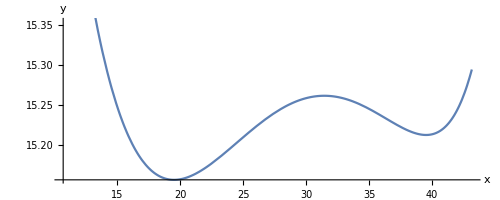
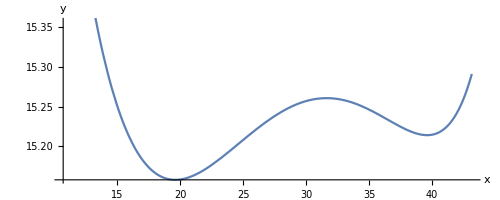
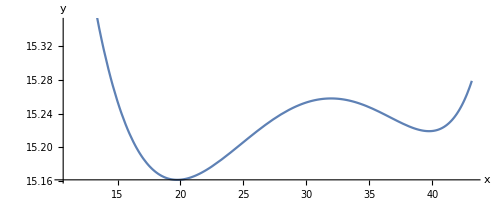
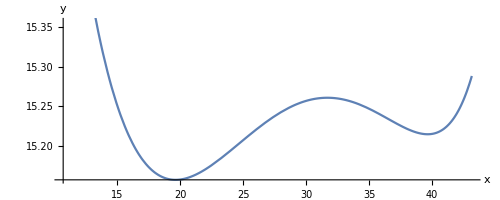
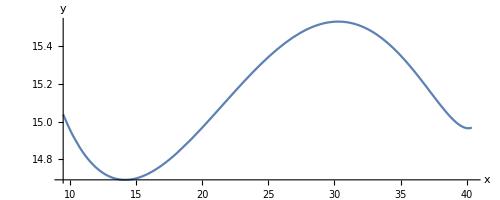
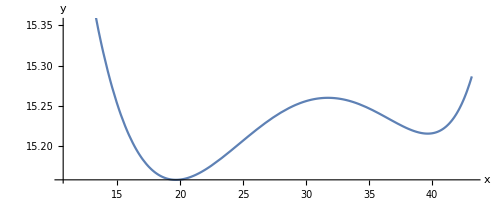
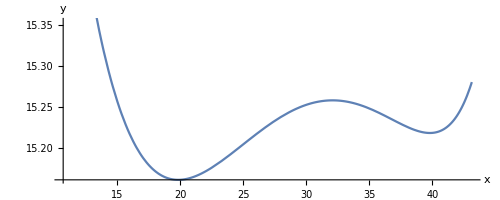
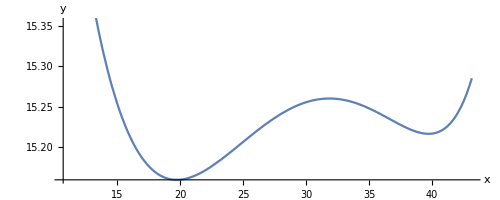
{192.828,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing@Table[ParametricPlot[{{Pol3[q][[2,1]]/.Last@sol[[2,i]],Pol3[q][[2,2]]/.Last@sol[[2,i]]}},{q,qmin,qmax},AxesLabel->{"x","y"},PlotLegends->Automatic],{i,1,20}]
```

Dal Table prendo la soluzione che più si avvicina ad una retta parallela all’asse x

```mathematica
paramsol = 11;
```

```mathematica
Manipulate[
	Show[
		ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]}/.Last@sol[[2,paramsol]],{Pol4[q][[2,1]],Pol4[q][[2,2]]}}/.Last@sol[[2,paramsol]],{q,qmin,qmax},PlotStyle->Directive[Black,Dashed],PlotRange->{{-30,50},{0,50}}],
		ListPlot[{Pol1[q][[3]]/.Last@sol[[2,paramsol]],Pol2[q][[3]]/.Last@sol[[2,paramsol]],Pol3[q]/.Last@sol[[2,paramsol]],Pol4[q]/.Last@sol[[2,paramsol]]},Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-30,50},{0,50}}]],{q,qmin,qmax}]
```

## Sintesi di Traiettoria senza Correlazione

```mathematica
data= Array[0,Length[Fdx]];
```

In un vettore inserisco rispettivamente i dati delle coordinate x e i rispettivi valori del movente.

```mathematica
For[i=1,i <= Length[Fdx],i++,data[[i]]={Fdx[[i]],rangemedia[[i]]}];data;
```

Ora svolgo un fitting dei dati per ottenere il moto della gru in funzione della posizione x. 
Applico sia un modello lineare che polinomiale.

```mathematica
lm=LinearModelFit[data,x,x]
poli = Fit[data, {1,x,x^2,x^3}, x]
```

FittedModel[1.41737-0.0152597 x]

1.18586+0.00560664 x-0.000497271 x^2+2.80518×10^-6 x^3

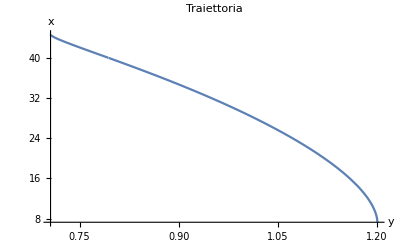

```mathematica
Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,LvP = L1P ,xvD=xDD,yvD=yDD},Plot[Pol3[q][[2,1]],{q,qmin,qmax},PlotLabel->"Traiettoria",AxesLabel->{"y","x"}]]
```

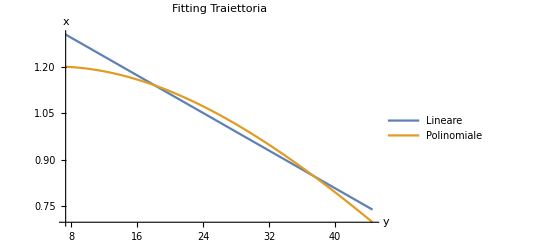

```mathematica
Plot[{lm[x],poli},{x,Last@Fdx,First@Fdx},PlotLabel->"Fitting Traiettoria",AxesLabel->{"y","x"},PlotLegends->{"Lineare","Polinomiale"}]
```

```mathematica
range = Range[Last@Fdx,First@Fdx,(First@Fdx-Last@Fdx)/100]
```

{7.29908,7.67181,8.04455,8.41728,8.79001,9.16275,9.53548,9.90821,10.2809,10.6537,11.0264,11.3991,11.7719,12.1446,12.5173,12.8901,13.2628,13.6355,14.0083,14.381,14.7537,15.1265,15.4992,15.8719,16.2447,16.6174,16.9901,17.3629,17.7356,18.1083,18.4811,18.8538,19.2266,19.5993,19.972,20.3448,20.7175,21.0902,21.463,21.8357,22.2084,22.5812,22.9539,23.3266,23.6994,24.0721,24.4448,24.8176,25.1903,25.563,25.9358,26.3085,26.6812,27.054,27.4267,27.7994,28.1722,28.5449,28.9176,29.2904,29.6631,30.0358,30.4086,30.7813,31.154,31.5268,31.8995,32.2722,32.645,33.0177,33.3904,33.7632,34.1359,34.5086,34.8814,35.2541,35.6268,35.9996,36.3723,36.745,37.1178,37.4905,37.8632,38.236,38.6087,38.9814,39.3542,39.7269,40.0996,40.4724,40.8451,41.2178,41.5906,41.9633,42.336,42.7088,43.0815,43.4542,43.827,44.1997,44.5724}

```mathematica
fFxl[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Pol3[Table[lm[x],{x,range}]][[2,2]];
```

Applico dunque la funzione penalità sui valori ottenuti tramite la fuzione linearizzata.

```mathematica
penaltyfFxl[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Total[Abs[fFxl[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD]-Fdy]];
```

```mathematica
sol2=Timing@Table[NMinimize[{penaltyfFxl[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD],5<Lv1,5<Lv2,10<Lv3,2<Lv4,20<Lv5,2<Lv6,15 < LvP,-15<xvD,5<yvD
},{Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD}∈Reals,AccuracyGoal->5, PrecisionGoal->5,Method->{"NelderMead","RandomSeed"->i}],{i,1,20}]
```

{794.094,{{0.859755,{Lv1→9.8948,Lv2→12.9321,Lv3→15.7662,Lv4→3.99714,Lv5→22.7924,Lv6→5.32685,LvP→19.2951,xvD→-8.25417,yvD→6.06746}},{1.3066,{Lv1→10.0102,Lv2→11.6284,Lv3→17.2254,Lv4→4.03197,Lv5→20.8599,Lv6→6.28298,LvP→15.9084,xvD→-6.43881,yvD→8.50478}},{1.13125,{Lv1→12.8586,Lv2→12.5648,Lv3→20.4068,Lv4→3.79778,Lv5→25.7026,Lv6→7.74371,LvP→18.9715,xvD→-6.49692,yvD→9.34966}},{1.21296,{Lv1→8.49046,Lv2→15.1646,Lv3→15.5297,Lv4→6.15158,Lv5→20.6948,Lv6→5.01927,LvP→17.8522,xvD→-10.2055,yvD→9.0544}},{1.1223,{Lv1→9.01267,Lv2→9.09779,Lv3→16.8799,Lv4→3.03384,Lv5→20.3005,Lv6→5.61935,LvP→16.3476,xvD→-5.00492,yvD→5.88213}},{9.3736,{Lv1→10.3602,Lv2→15.2316,Lv3→11.9244,Lv4→7.91486,Lv5→20.1435,Lv6→6.58279,LvP→16.5338,xvD→-13.9331,yvD→6.48724}},{20.6327,{Lv1→14.2037,Lv2→8.97541,Lv3→14.6811,Lv4→10.9617,Lv5→20.0776,Lv6→16.0753,LvP→25.0019,xvD→-14.1953,yvD→6.28857}},{0.895241,{Lv1→6.59086,Lv2→13.9176,Lv3→14.102,Lv4→6.10068,Lv5→20.1772,Lv6→3.1258,LvP→20.5382,xvD→-10.5929,yvD→5.89547}},{13.4507,{Lv1→8.94949,Lv2→9.21393,Lv3→17.8092,Lv4→8.2378,Lv5→20.,Lv6→6.32415,LvP→18.4266,xvD→-8.09067,yvD→10.1233}},{1.43652,{Lv1→17.2436,Lv2→13.692,Lv3→21.8515,Lv4→5.46047,Lv5→24.2357,Lv6→11.6534,LvP→24.2258,xvD→-5.2474,yvD→14.0173}},{1.74038,{Lv1→16.6461,Lv2→17.2469,Lv3→15.4915,Lv4→7.15214,Lv5→20.2988,Lv6→11.2351,LvP→15.9123,xvD→-10.4119,yvD→18.0209}},{14.3016,{Lv1→7.36651,Lv2→9.60465,Lv3→16.9163,Lv4→8.07755,Lv5→20.,Lv6→6.56152,LvP→16.2903,xvD→-10.3927,yvD→7.71738}},{1.18543,{Lv1→5.31182,Lv2→17.5212,Lv3→13.5284,Lv4→7.32873,Lv5→21.0538,Lv6→2.40964,LvP→15.5012,xvD→-14.3041,yvD→6.53587}},{1.21362,{Lv1→5.37353,Lv2→7.22937,Lv3→23.2136,Lv4→5.01604,Lv5→20.4055,Lv6→7.44795,LvP→20.9967,xvD→-6.35974,yvD→9.53042}},{1.37219,{Lv1→5.00471,Lv2→8.94903,Lv3→24.2366,Lv4→5.51656,Lv5→20.3237,Lv6→8.78941,LvP→20.273,xvD→-7.9514,yvD→11.5319}},{1.37563,{Lv1→9.29503,Lv2→14.1116,Lv3→14.5383,Lv4→5.59827,Lv5→20.,Lv6→5.0442,LvP→16.5439,xvD→-9.55575,yvD→8.75717}},{1.42391,{Lv1→6.23037,Lv2→5.93719,Lv3→22.1306,Lv4→2.79785,Lv5→23.9012,Lv6→3.35567,LvP→20.2491,xvD→-3.27081,yvD→5.}},{1.39959,{Lv1→8.02545,Lv2→8.1045,Lv3→19.7813,Lv4→3.24691,Lv5→20.8692,Lv6→5.04133,LvP→16.0359,xvD→-3.76346,yvD→7.33935}},{1.28667,{Lv1→7.57357,Lv2→7.94572,Lv3→21.6881,Lv4→6.8115,Lv5→20.,Lv6→15.6246,LvP→19.4614,xvD→-14.3854,yvD→13.1145}},{1.1504,{Lv1→6.71456,Lv2→11.9324,Lv3→17.4817,Lv4→5.58058,Lv5→20.5008,Lv6→3.76408,LvP→19.7181,xvD→-7.91293,yvD→7.82226}}}}

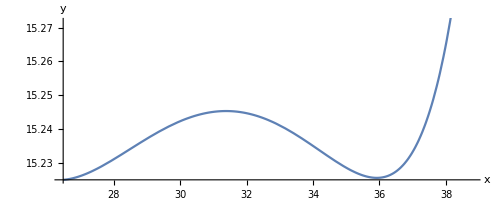
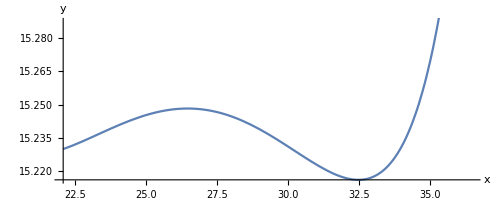
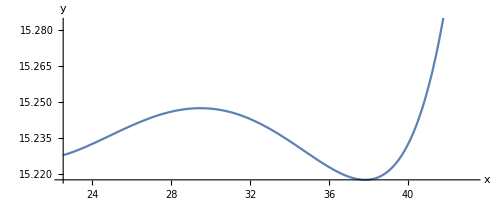
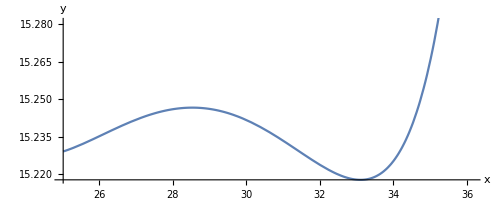
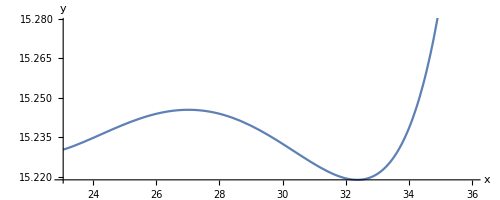
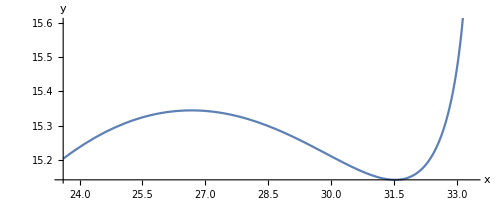
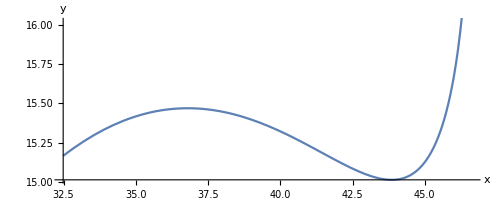
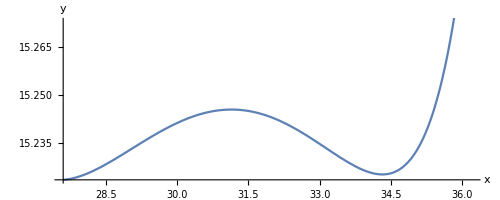
{153.938,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing@Table[ParametricPlot[{{Pol3[q][[2,1]]/.Last@sol2[[2,i]],Pol3[q][[2,2]]/.Last@sol2[[2,i]]}},{q,qmin,qmax},AxesLabel->{"x","y"},PlotLegends->Automatic],{i,1,20}]
```

```mathematica
paramsol2 = 10;
```

```mathematica
Manipulate[
	Show[
		ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]}/.Last@sol2[[2,paramsol2]],{Pol4[q][[2,1]],Pol4[q][[2,2]]}}/.Last@sol2[[2,paramsol2]],{q,qmin,qmax},PlotStyle->Directive[Black,Dashed],PlotRange->{{-30,70},{0,50}}],
		ListPlot[{Pol1[q][[3]]/.Last@sol2[[2,paramsol2]],Pol2[q][[3]]/.Last@sol2[[2,paramsol2]],Pol3[q]/.Last@sol2[[2,paramsol2]],Pol4[q]/.Last@sol2[[2,paramsol2]]},Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-30,70},{0,50}}]],{q,qmin,qmax}]
```

```mathematica
fFxpoli[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Pol3[Table[poli,{x,range}]][[2,2]];
```

Applico dunque la funzione penalità sui valori ottenuti tramite la fuzione fittata nella polinomiale.

```mathematica
penaltyfFxpoli[Lv1_,Lv2_,Lv3_,Lv4_,Lv5_,Lv6_,LvP_,xvD_,yvD_]:=Total[Abs[fFxpoli[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD]-Fdy]];
```

```mathematica
sol3=Timing@Table[NMinimize[{penaltyfFxpoli[Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD],5<Lv1,5<Lv2,10<Lv3,2<Lv4,20<Lv5,2<Lv6,15 < LvP,-15<xvD,5<yvD
},{Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,LvP,xvD,yvD}∈Reals,AccuracyGoal->5, PrecisionGoal->5,Method->{"NelderMead","RandomSeed"->i}],{i,1,20}]
```

{747.641,{{1.49504,{Lv1→11.1615,Lv2→12.6937,Lv3→15.8221,Lv4→4.61788,Lv5→20.9747,Lv6→6.88273,LvP→19.689,xvD→-7.6151,yvD→7.96706}},{1.95998,{Lv1→11.3294,Lv2→10.825,Lv3→18.1617,Lv4→3.23851,Lv5→21.4899,Lv6→7.85829,LvP→15.9542,xvD→-5.21524,yvD→7.94078}},{1.42401,{Lv1→11.397,Lv2→9.70514,Lv3→21.6426,Lv4→3.27269,Lv5→22.9555,Lv6→7.82606,LvP→15.9652,xvD→-3.72072,yvD→9.51982}},{5.75871,{Lv1→5.44988,Lv2→16.2718,Lv3→13.9816,Lv4→8.82743,Lv5→20.1616,Lv6→3.00477,LvP→15.7909,xvD→-14.7218,yvD→6.61221}},{1.06277,{Lv1→8.73016,Lv2→9.8259,Lv3→19.4457,Lv4→2.77139,Lv5→23.2857,Lv6→6.22275,LvP→19.776,xvD→-4.99181,yvD→5.}},{1.92655,{Lv1→9.40278,Lv2→15.7214,Lv3→11.3819,Lv4→5.31334,Lv5→20.1681,Lv6→4.52743,LvP→15.2555,xvD→-11.7429,yvD→6.38542}},{15.3241,{Lv1→12.8218,Lv2→9.73621,Lv3→14.9298,Lv4→10.0185,Lv5→20.,Lv6→14.9179,LvP→22.3064,xvD→-14.6663,yvD→6.17092}},{1.82511,{Lv1→12.2946,Lv2→17.0178,Lv3→13.1769,Lv4→7.23248,Lv5→20.,Lv6→7.39618,LvP→21.617,xvD→-11.5654,yvD→10.4401}},{1.19525,{Lv1→11.4965,Lv2→11.6349,Lv3→22.3903,Lv4→3.74852,Lv5→25.8559,Lv6→7.17318,LvP→16.9426,xvD→-5.65571,yvD→10.1342}},{4.66265,{Lv1→5.00813,Lv2→10.2046,Lv3→21.9384,Lv4→8.36332,Lv5→20.,Lv6→4.28502,LvP→24.8849,xvD→-7.10736,yvD→11.6673}},{0.979521,{Lv1→10.6265,Lv2→9.72515,Lv3→23.55,Lv4→6.94572,Lv5→20.4941,Lv6→19.3811,LvP→20.8794,xvD→-14.8751,yvD→15.7599}},{1.60863,{Lv1→8.82905,Lv2→9.15781,Lv3→22.7642,Lv4→3.27963,Lv5→22.4564,Lv6→6.10565,LvP→16.2225,xvD→-2.92386,yvD→9.18839}},{1.15082,{Lv1→5.30831,Lv2→17.5592,Lv3→13.9525,Lv4→7.1942,Lv5→21.7507,Lv6→2.32282,LvP→15.9718,xvD→-14.2969,yvD→6.49911}},{9.783,{Lv1→5.85756,Lv2→9.62701,Lv3→18.2436,Lv4→7.51687,Lv5→20.243,Lv6→5.58677,LvP→15.8901,xvD→-9.99613,yvD→8.03107}},{9.45689,{Lv1→7.37034,Lv2→9.07469,Lv3→18.6862,Lv4→7.86727,Lv5→20.,Lv6→6.26777,LvP→17.7136,xvD→-8.63481,yvD→9.74345}},{0.783353,{Lv1→8.74429,Lv2→20.7753,Lv3→16.9542,Lv4→4.62799,Lv5→29.9042,Lv6→5.51501,LvP→16.3537,xvD→-14.3258,yvD→6.41946}},{0.686374,{Lv1→9.23285,Lv2→18.0751,Lv3→12.9077,Lv4→8.13227,Lv5→20.8719,Lv6→5.09754,LvP→27.6899,xvD→-13.4333,yvD→7.74228}},{239.388,{Lv1→23.2019,Lv2→10.8571,Lv3→11.1481,Lv4→16.1634,Lv5→38.1503,Lv6→7.74893,LvP→15.,xvD→11.9875,yvD→5.18908}},{2.26948,{Lv1→15.3443,Lv2→13.3728,Lv3→24.3191,Lv4→7.51636,Lv5→23.5303,Lv6→9.36337,LvP→30.5935,xvD→-3.89769,yvD→16.3747}},{0.967912,{Lv1→7.60953,Lv2→16.8697,Lv3→21.279,Lv4→6.78604,Lv5→26.7291,Lv6→4.07993,LvP→20.9285,xvD→-11.1193,yvD→10.9839}}}}

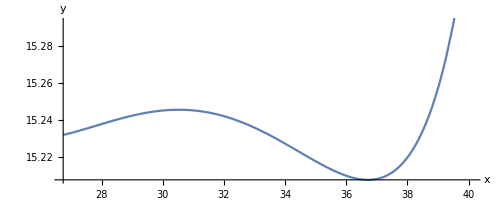
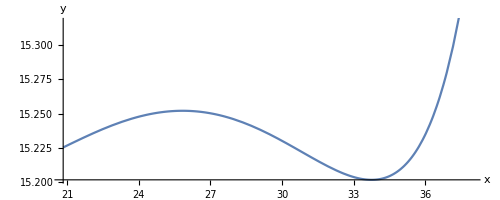
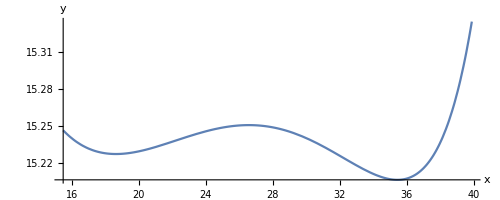
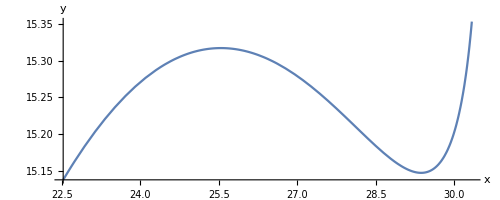
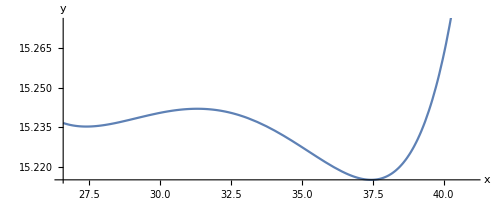
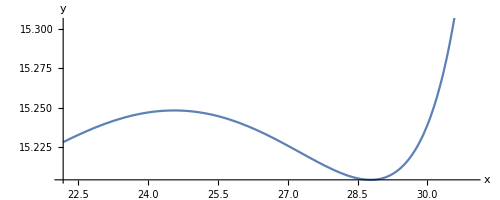
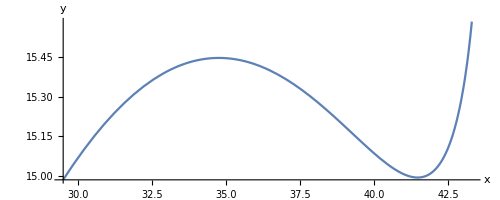
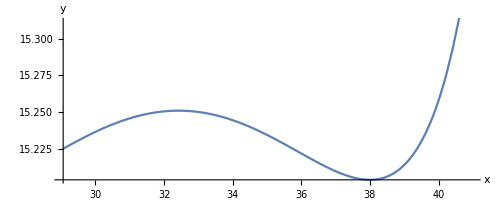
{164.359,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing@Table[ParametricPlot[{{Pol3[q][[2,1]]/.Last@sol3[[2,i]],Pol3[q][[2,2]]/.Last@sol3[[2,i]]}},{q,qmin,qmax},AxesLabel->{"x","y"},PlotLegends->Automatic],{i,1,20}]
```

```mathematica
paramsol3 = 9;
```

```mathematica
Manipulate[
	Show[
		ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]}/.Last@sol3[[2,paramsol3]],{Pol4[q][[2,1]],Pol4[q][[2,2]]}}/.Last@sol3[[2,paramsol3]],{q,qmin,qmax},PlotStyle->Directive[Black,Dashed],PlotRange->{{-30,70},{0,50}}],
		ListPlot[{Pol1[q][[3]]/.Last@sol3[[2,paramsol3]],Pol2[q][[3]]/.Last@sol3[[2,paramsol3]],Pol3[q]/.Last@sol3[[2,paramsol3]],Pol4[q]/.Last@sol3[[2,paramsol3]]},Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-30,70},{0,50}}]],{q,qmin,qmax}]
```

Di seguito effettuo il plot dei migliori risutati ottenuti con ogni metodo applicato

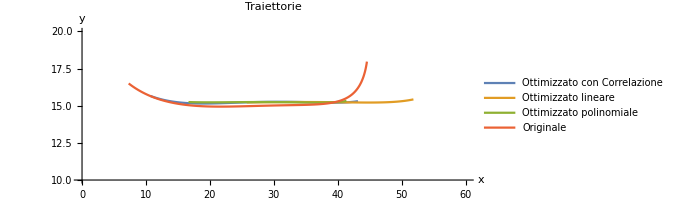

```mathematica
ParametricPlot[{{Pol3[q][[2,1]]/.Last@sol[[2,paramsol]],Pol3[q][[2,2]]/.Last@sol[[2,paramsol]]},{Pol3[q][[2,1]]/.Last@sol2[[2,paramsol2]],Pol3[q][[2,2]]/.Last@sol2[[2,paramsol2]]},{Pol3[q][[2,1]]/.Last@sol3[[2,paramsol3]],Pol3[q][[2,2]]/.Last@sol3[[2,paramsol3]]}
,{Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,LvP = L1P ,xvD=xDD,yvD=yDD},Pol3[q][[2,1]]],Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,LvP = L1P ,xvD=xDD,yvD=yDD},Pol3[q][[2,2]]]}},{q,qmin,qmax},AxesLabel->{"x","y"}, PlotRange->{{0,60},{10,20}},PlotLabel->"Traiettorie",PlotLegends->{"Ottimizzato con Correlazione","Ottimizzato lineare","Ottimizzato polinomiale","Originale"}]
```